## Cold alkali-atom multi-channel scattering with Mathematica

See the notes “ScatteringTheoryNotes-NPM-2019.nb” for an earlier version of this scattering code with the theory background.  See “LiPotentials.nb” for the background on the hyperfine and Zeeman matrix elements and projection operators. Here, I’m copying over the relevant modules to have a more compact notebook with only the code, and minimal exposition.

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μ=mLi7/2;
```

### Morse/Long-Range Potential For Lithium (Coded by A. Laskowski, See Le Roy et al)

```mathematica
ypeq[p_,r_]:= (r^p - 1^p)/(r^p +1^p);
ypref[p_,r_]:= (r^p - 1.5^p)/(r^p +1.5^p);
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DTT[r_,m_,btt_,ρ_,s_]:= 1-Exp[-btt ρ r]*Sum[(btt ρ r)^k/(k!),{k,0,m-1+s}];
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,0.54,-1];
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
t10 = 2.78683*10^9;
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
β[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

```mathematica
βinfT=βinf[tde,tre,DDSTriplet[6,tre],DDSTriplet[8,tre],DDSTriplet[10,tre],tc6,tc8,t10]
```

-0.509836

```mathematica
βTriplet[r_]:= βinfT*y[tref,r,5]+(1-y[tref,r,5])*Sum[tβcf[[j+1]]*y[tref,r,3]^j,{j,0,Length[tβcf]-1}];
ulrTriplet[r_]:= DDSTriplet[6,r] tc6/r^6+DDSTriplet[8,r] tc8/r^8+DDSTriplet[10,r] t10/r^10;
TripletMLR[r_]:= tde(1-ulrTriplet[r]/ulrTriplet[tre]*Exp[-βTriplet[r]*y[tre,r,p]])^2-tde;
```

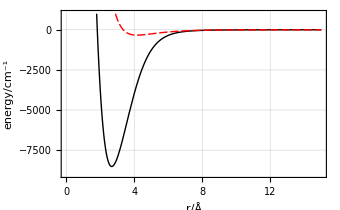

```mathematica
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
SingletMLR[r_]:= VMLR[r,sre,sde,β[r,sβcf1,βinf[sde,sre,1,1,1,C6,C8,C10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,C6,C8,C10]
Plot[{SingletMLR[r],TripletMLR[r]},{r,1.5,15},Frame->True,FrameLabel->{"r/Å","energy/cm^-1"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-9000,1000}]
```

#### Create an interpolated function to evaluate this fast

```mathematica
Rmax=300; (*bohr*)
Rmin=2.0;
NR =300;
dR=(Rmax-Rmin)/(NR-1);
RGrid =Table[Rmin+((iR-1)/(NR-1))^4(Rmax-Rmin),{iR,1,NR}];Length[RGrid]
```

300

```mathematica
TripletMLRHBdat = Table[{RGrid[[i]],invcminHartree*TripletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
TripletHBMLR=Interpolation[TripletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
SingletMLRHBdat = Table[{RGrid[[i]],invcminHartree*SingletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
SingletHBMLR=Interpolation[SingletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
```

General::munfl: Exp[-726.698] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-747.252] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-768.319] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

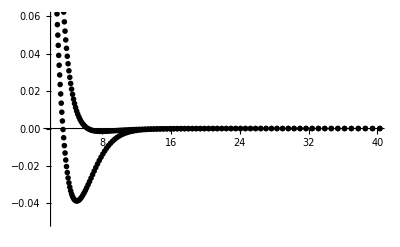

```mathematica
ListPlot[{SingletMLRHBdat,TripletMLRHBdat},PlotRange->{{Rmin,40},{-0.05,.06}}]
```

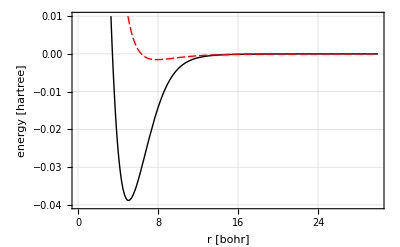

```mathematica
Plot[{SingletHBMLR[r],TripletHBMLR[r]},{r,Rmin,30},Frame->True,FrameLabel->{"r [bohr]","energy [hartree]"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-0.04,0.01}]
```

### Hyperfine & Zeeman Matrix Elements

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;
Li7AH =401.7520435*MHzPerHartree; (*MHz -> Hartree*)
Li6AH = 152.136840720*MHzPerHartree;  (*MHz -> Hartree*)
μbH = 1.3996244936142*MHzPerHartree;   (*MHz/G  ->  Hartree/G*)
μnH = 7.62259328547*10^-4*MHzPerHartree;(* MHz/G -> Hartree/G *)
```

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

For M_T=2

Unsymmetrized Basis

```mathematica
mF2unsym =Select[f1m1f2m2basis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

```mathematica
mF2basis = {{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,2,1}};
```

Use the following line and skip the lengthy projection operator calculation if you only want Li-7 M_F=2.

```mathematica
SymSingletProjLi7MF2={{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}};
SymTripletProjLi7MF2={{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}};
```

```mathematica
(*ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];*)

(*ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];*)
```

```mathematica
(*SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

```mathematica
(*SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]*)
```

```mathematica
(*SProjSymLi7=FullSimplify[SingletProjectionSym[0,0]]*)
```

```mathematica
(*MatrixForm[N[SProjSymLi7]]*)
```

```mathematica
(*TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

For symmetrized basis:

```mathematica
(*TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]),{j,1,5},{jp,1,5}] *)
```

```mathematica
(*TProjSymLi7=FullSimplify[TripletProjectSym[0,0]];*)
```

```mathematica
(*TProjSymLi7*)
```

```mathematica
(*MatrixForm[N[TProjSymLi7]]*)
```

(s i)f'm' H^HZ(s i)f m=A^HF/2[f(f+1)-s(s+1)-i(i+1)]δ_ff' δ_mm'+g_s μ_B B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_s(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'+g_i μ_N B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_i(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B √((2fp+1)(2f+1))Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B √((2fp+1)(2f+1))Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√((1+δ_αβ)(1+δ_α'β')))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
Eigensystem[FullSimplify[HZsym[0,0,B]]/.B->0][[1]]HartreePerMHz
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

{-1004.38,602.628,602.628,-200.876,-200.876}

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
Htest[r_,B_]:= HZsymLi7[B]+SymTripletProjLi7MF2*TripletHBMLR[r]+SymSingletProjLi7MF2*SingletHBMLR[r];
```

```mathematica
ValVecs[B_]:=Table[ Sort[Transpose[Eigensystem[Htest[RGrid [[iR]],B]]]],{iR,1,NR}];
```

```mathematica
AdiabaticUV=Table[{{RGrid[[iR]],ValVecs[0.0][[iR,n,1]]},ValVecs[0.0][[iR,n,2]]},{iR,1,NR},{n,1,5}];
```

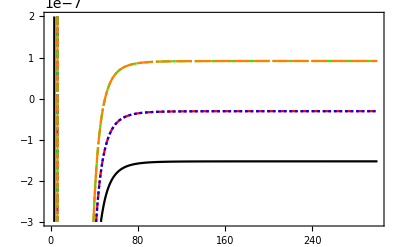

```mathematica
padiabatic=ListPlot[Table[AdiabaticUV[[1;;NR,n,1]],{n,1,5}],Joined->True,PlotMarkers->None,Frame->True,PlotRange->{-3 10^-7,2 10^-7},PlotStyle->{Black,Red,Blue,Green,Orange}]
```

```mathematica
Clear[Eth,AsymC];AsymC[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[2]];
Eth[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[1]];
```

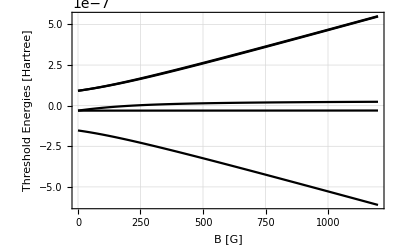

```mathematica
Plot[Flatten[{Eth[B]},1],{B,0,1200},PlotRange->All,Frame->True,GridLines->{Automatic},GridLinesStyle->Directive[Thin] ,FrameLabel->{"B [G]","Threshold Energies [Hartree]"}]
```

```mathematica
VR[r_,B_]:=AsymC[B]. HZsymLi7[B].Transpose[AsymC[B]]+AsymC[B].SymTripletProjLi7MF2.Transpose[AsymC[B]]*TripletHBMLR[r]+AsymC[B].SymSingletProjLi7MF2.Transpose[AsymC[B]]*SingletHBMLR[r];
```

```mathematica
Vmattest[r]=VR[r,0.0];
```

Find the value of RGrid near R=50 bohr or so.

```mathematica
Position[RGrid,x_/;x>60.0][[1,1]]
```

200

```mathematica
LongRangePots=Table[AdiabaticUV[[Position[RGrid,x_/;x>50.0][[1,1]];;NR,n,1]],{n,1,5}];
```

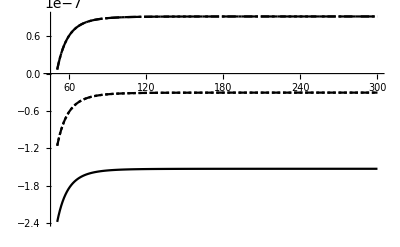

```mathematica
ListPlot[LongRangePots,Joined->True,PlotMarkers->None]
```

```mathematica
LongRangeParsols=Table[FindFit[LongRangePots[[n]],Ethfit-Cfit6/r^6-Cfit8/r^8-Cfit10/r^10,{Ethfit,Cfit6,Cfit8,Cfit10},r],{n,1,5}];
LongRangePars=Mean[Table[{Ethfit,Cfit6,Cfit8,Cfit10}/.LongRangeParsols[[n]],{n,1,5}]]
```

{-6.10595×10^-9,1393.93,83423.4,7.73338×10^6}

```mathematica
VLongRange[LongRangePars_,r_]:=LongRangePars[[1]]-LongRangePars[[2]]/r^6-LongRangePars[[3]]/r^8-LongRangePars[[4]]/r^10
```

These values are in atomic units.  Let’s compare them to the converted values used in the model.

```mathematica
LongRangePars={0, C6 invcminHartree AngstrominBohr^6,C8 invcminHartree AngstrominBohr^8,C10 invcminHartree AngstrominBohr^10}
```

{0,1393.39,83425.5,7.37211×10^6}

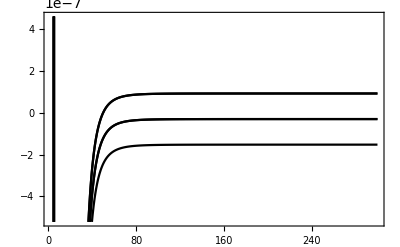

```mathematica
protated=Plot[Table[{Vmattest[r][[n,n]]},{n,1,5}],{r,Rmin,Rmax}(*PlotRange->{-3 10^-7,2 10^-7}*),Frame->True]
```

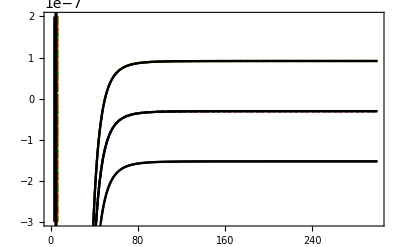

```mathematica
Show[{padiabatic,protated}]
```

### Import the data from the full coupled-channels calculation using Johnson’s log-derivative method in FORTRAN

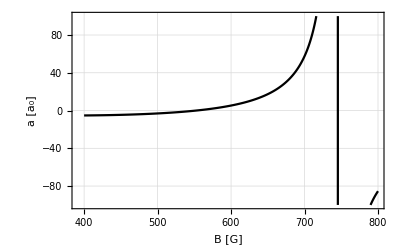

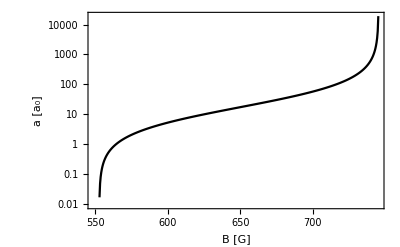

```mathematica
Li7FRData=Import["/Users/niravmehta/Documents/GitHub/LiScattering/Li7FR.dat", "Data"];
p0=ListPlot[Li7FRData,Joined->True,PlotMarkers->None,Frame->True,PlotRange->{-100,100},FrameLabel->{"B [G]","a [a_0]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin]
p1=ListLogPlot[Li7FRData,Joined->True,PlotMarkers->None,Frame->True(*PlotRange->{{540,750},{0,3000}}*),FrameLabel->{"B [G]","a [a_0]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin]
```

PRL 102, 090402 (2009) reports the resonance pole of the scattering length to be at 736.8(2) G.  The zero of the scattering length to be at approximately 544 G

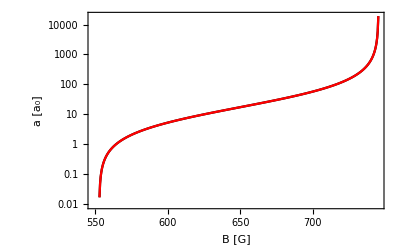

```mathematica
Li7FRData=Import["/Users/niravmehta/Documents/GitHub/LiScattering/Li7FR.dat", "Data"];
p2=ListLogPlot[Li7FRData,Joined->True,PlotStyle->Red,PlotMarkers->None,Frame->True(*PlotRange->{{540,750},{0,3000}}*),FrameLabel->{"B [G]","a [a_0]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin];
Show[p1,p2]
```

This calculation gives the pole position at about 745 G and the zero at about 540 G

```mathematica
sigma = Table[{Li7FRData[[i,1]],(Li7FRData[[i,2]]BohrinAngstrom 10^8)^2 4π},{i,1,Length[Li7FRData]}];
```

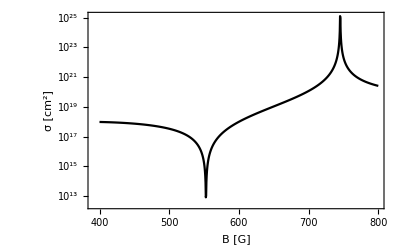

```mathematica
ListLogPlot[sigma,PlotStyle->Black,Joined->True,PlotMarkers->None,Frame->True(*PlotRange->{{540,750},{0,3000}}*),FrameLabel->{"B [G]","σ [cm^2]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin]
```

### QDT

```mathematica
SymSingletProjLi7MF2={{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}};
SymTripletProjLi7MF2={{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}};
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B √((2fp+1)(2f+1))Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B √((2fp+1)(2f+1))Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√((1+δ_αβ)(1+δ_α'β')))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
Clear[Eth,AsymC];
AsymC[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[2]];
Eth[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[1]];
```

```mathematica
μdefect[s_]:=Which[s==0,-0.00872,s==1,0.07484]
```

```mathematica
KSRhf=FullSimplify[SymSingletProjLi7MF2*Tan[π μ0] + SymTripletProjLi7MF2*Tan[π μ1]];MatrixForm[KSRhf]
```

(1/4 (Tan[π μ0]+3 Tan[π μ1]) | 1/8 √3 (-Tan[π μ0]+Tan[π μ1]) | (-Tan[π μ0]+Tan[π μ1])/(4 √2) | 1/4 (-Tan[π μ0]+Tan[π μ1]) | 1/8 √3 (Tan[π μ0]-Tan[π μ1])
1/8 √3 (-Tan[π μ0]+Tan[π μ1]) | 1/16 (3 Tan[π μ0]+13 Tan[π μ1]) | 1/8 √(3/2) (Tan[π μ0]-Tan[π μ1]) | 1/8 √3 (Tan[π μ0]-Tan[π μ1]) | -3/16 (Tan[π μ0]-Tan[π μ1])
(-Tan[π μ0]+Tan[π μ1])/(4 √2) | 1/8 √(3/2) (Tan[π μ0]-Tan[π μ1]) | 1/8 (Tan[π μ0]+7 Tan[π μ1]) | (Tan[π μ0]-Tan[π μ1])/(4 √2) | 1/8 √(3/2) (-Tan[π μ0]+Tan[π μ1])
1/4 (-Tan[π μ0]+Tan[π μ1]) | 1/8 √3 (Tan[π μ0]-Tan[π μ1]) | (Tan[π μ0]-Tan[π μ1])/(4 √2) | 1/4 (Tan[π μ0]+3 Tan[π μ1]) | 1/8 √3 (-Tan[π μ0]+Tan[π μ1])
1/8 √3 (Tan[π μ0]-Tan[π μ1]) | -3/16 (Tan[π μ0]-Tan[π μ1]) | 1/8 √(3/2) (-Tan[π μ0]+Tan[π μ1]) | 1/8 √3 (-Tan[π μ0]+Tan[π μ1]) | 1/16 (3 Tan[π μ0]+13 Tan[π μ1]))

I. Define zero-energy solution and Riccati functions

```mathematica
Clear[l,r,rp];
χminus[r_,l_]= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2)];
χmprime[r_,l_]= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]=(*√((2 μ k)/π)*)r SphericalBesselJ[l,k r];
g[l_,k_,r_]=(*√((2 μ k)/π)*)r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]=Simplify[D[f[l,k,rp],rp]]/.rp->r; 
dgdr[l_,k_,r_]=Simplify[D[g[l,k,rp],rp]]/. rp->r;
```

II. Define reference wave-function base pairs

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=-α[r]Cos[ϕ+phaseint[r]];
f0=α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

III. Calculate alpha and phase integral functions using the Milne method. These will then be used for constructing the reference wave functions f^o and g^o in the long range-region.

```mathematica
CalcAlphaPhaseIntFun[Ε_,l_,nr_,μ_,V_,rx_,rf_,r_]:= Module[{k,BC1,BC2,asol,rGrid,PhaseIntTable,rp,PhaseIntFun,αfun,α},
k=Sqrt[2 μ (Ε-V[r])];
BC1 = 1/Sqrt[k^(1/2)]/.r->rx;
BC2 = D[1/Sqrt[k^(1/2)],r]/.r->rx;
asol = NDSolve[{α''[r] + k^2 α[r] -1/α[r]^3== 0, α[rx] == BC1, α'[rx] == BC2},α,{r,rx,rf}];
rGrid = Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable = Flatten[{0,Table[NIntegrate[1/α[rp]^2/.asol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
PhaseIntFun = Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[1;;i]]]},{i,1,nr}]];
αfun = α/.asol;
Flatten[{αfun,PhaseIntFun}]
];
```

```mathematica
CalcY[Ε_,l_,μ_,V_,rmin_,rmax_]:=Module[{Y,u,up,rp,r},
u=NDSolveValue[{-1/(2 μ)u''[r]+ V[r]*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up[r_] = D[u[rp],rp]/.rp->r;
Y = up[r]/u[r]/.r->rmax;
Return[Y]
]
```

```mathematica
Vlr[r_]:=VLongRange[LongRangePars,r]
```

```mathematica
ksqr[Ε_,l_,r_,μ_] := 2μ(Ε-(Vlr[r]+(l(l+1))/(2 μ r^2)));
BC1[Ε_,l_,r_,rx_,μ_] := 1/ksqr[Ε,l,r,μ]^(1/4)/.r->rx;
BC2[Ε_,l_,r_,rx_,μ_] := D[1/ksqr[Ε,l,r,μ]^(1/4),r]/.r->rx;
Εtest=10.^-16;
rx=10.0; (*Location where WKB BC's are imposed on the Milne solution*)
rf=250; (*Location where Milne solution is matched to Bessel functions to give phase shift*)
ltest=0;
```

```mathematica
ksqr[Εtest,ltest,r,μ]
```

12789.4 (1.×10^-16+(7.37211×10^6)/r^10+83425.5/r^8+1393.39/r^6)

```mathematica
BC1[Εtest,ltest,r,rx,μ]
```

0.402983

```mathematica
(*This next bit of code finds the constant phases Subscript[ϕ, i] that "standardize" the MQDT".  
They ensure that the reference functions maintain maximal linear independence under the centrifugal barrier*)
ltest=0;
lmax=2;Clear[α];
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Εtest,ltest,r,μ]α[r]-1/α[r]^3==0,α[rx]==BC1[Εtest,ltest,r,rx,μ],α'[rx]==BC2[Εtest,ltest,r,rx,μ]},α,{r,rx,rf}],{ltest,0,lmax}]];
α0fun=Table[α/.α0sol[[ltest+1]],{ltest,0,lmax}];
```

```mathematica
nr=300;
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,lmax}];
phaseintfuns=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,lmax}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,lmax}],{rf,rGrid}]];
ϕfinal=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
ϕfinal
```

{0.837914,-1.54452,-0.80453}

The base pair functions at zero energy are:

```mathematica
bp0=basepairs[ltest,ϕfinal[[ltest+1]],α0fun[[ltest+1]],phaseintfuns[[ltest+1]],r];
```

```mathematica
CalcCotGamma[l_,rx_,rf_,μ_,r_,ϵ_,ϕ_,Vlr_]:=Module[{nr,asol,phaseintfun,cotγ,gbound,gboundp,κ,f0,g0,f0p,g0p,χm,χmp},
κ=√Abs[2μ ϵ];
(*Ε_,l_,nr_,μ_,V_,rx_,rf_,r_*)
nr=300;
{asol,phaseintfun}= CalcAlphaPhaseIntFun[ϵ,l,nr,μ,Vlr,rx,rf,r];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,asol,phaseintfun,r];
(*gbound=√(2/π κ rp)BesselK[l+1/2,κ rp]/.rp->rf; 
gboundp=-((κ (rp κ BesselK[-1/2+l,rp κ]-BesselK[1/2+l,rp κ]+rp κ BesselK[3/2+l,rp κ]))/(√(2 π) √(rp κ)))/.rp->rf;*)
gbound = Exp[-κ r];
gboundp =- κ Exp[-κ r];
cotγ =(-gbound f0p - gboundp f0)/(gbound g0p-gboundp g0)/.r->rf;
Return[cotγ]
]
```

```mathematica
Plot[CalcCotGamma[ltest,rx,rf,μ,r,ϵ,ϕfinal[[1]],Vlr],{ϵ,-1,0}]
```

NDSolve::ndinnt: Initial condition 0.306651/(0.00296485+ϵ)^(1/8) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1/α$243977[rp$243977]^2/.NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{10.,10.}}.

ReplaceAll::reps: {NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1/α$243977[rp$243977]^2/.NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{10.,10.0001}}.

ReplaceAll::reps: {NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1/α$243977[rp$243977]^2/.NDSolve[{-1/α$243977[«1»]^3+12789.4 (Times[«2»]+Times[«2»]+Times[«2»]+ϵ) α$243977[r]+α$243977''[r]==0,α$243977[10.]==0.306651/(«22»+ϵ)^(1/8),α$243977'[10.]==0.000085887/(0.00296485+ϵ)^(9/8)},α$243977,{r,10.,250}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{10.0001,10.0002}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::nlim: rp$243977 = {10.,10.,10.0001,10.0002,10.0006,10.0011,10.0019,10.0031,«35»,10.7138,10.7648,10.8182,10.8739,10.9322,10.9929,11.0563,«250»}⟦«1»⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

### Scattering Asymptotic Functions

```mathematica
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
dse[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
dce[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

```mathematica
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
```

```mathematica
Nchan = 5;
Btest=0.0;
eps = 10^-15;
Etest=Eth[Btest][[1]]+eps
√(2μ(Etest-Eth[Btest][[1]]))
NumOpen[Energy_,B_]:=Count[Eth[B],u_/;u<Energy]
no = NumOpen[Etest,Btest]
```

-1.52649×10^-7

3.57623×10^-6

1

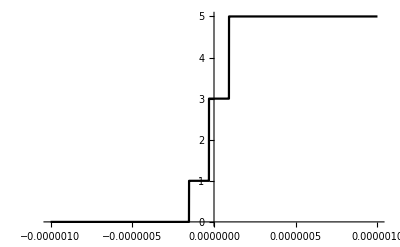

```mathematica
Plot[NumOpen[Energy,Btest],{Energy,-10^-6,10^-6}]
```